### Categorization

Tech Note

GSberveglieri/Phi4tools

GSberveglieri`Phi4tools`

GSberveglieri/Phi4tools/tutorial/FeynmanDiagramEvaluation

### Keywords

# Feynman Diagram Evaluation

In this Tech Note it is presented an example of how to compute the values of the diagrams in three dimensions starting from their integrands.

## Visualization

Let's consider, as an example, the diagrams of the Γ^(4)(0) at the order λ^4, i.e. with 4 quartic vertices with zero external momenta.

```mathematica
Needs["GSberveglieri`Phi4tools`"]
```

We use the function VisualizeDiagram to draw the graph of the Feynman diagrams contributing at the given order.

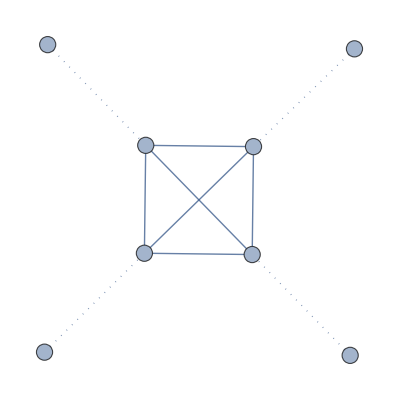
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
VisualizeDiagram[4,0,4]
```

It would be very challenging to numerically integrate directly the integrands written assigning the internal momenta to these diagrams. We have 3-loop diagrams, so the integrations would be generically in 6 dimensions (three integrations can be spared using the spherical symmetry of the integrand). It is helpful to substitute some of the analytically known subdiagrams so to reduce the number of effective loops and, thus, the dimension of the integrations.

Let's draw the effective diagrams after the substitutions implemented in this paclet. We do so by adding the option "Substitutions"→ "Analytics" to VisualizeDiagram.

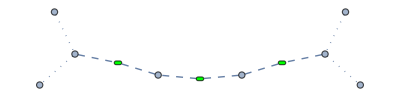
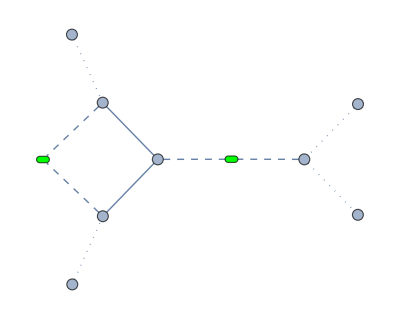
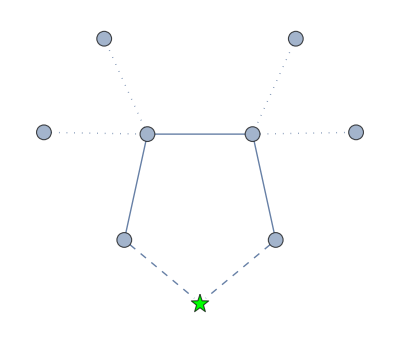
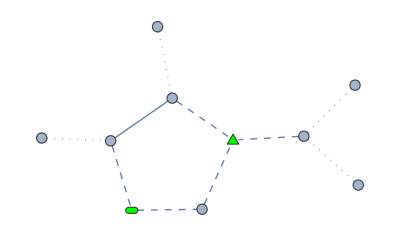
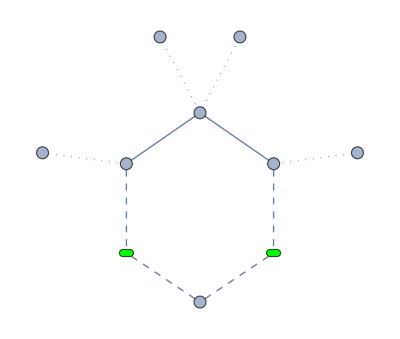
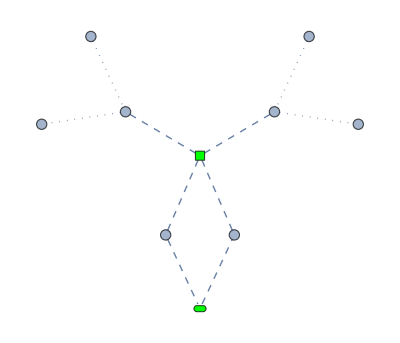
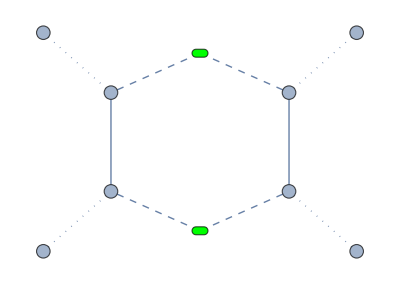
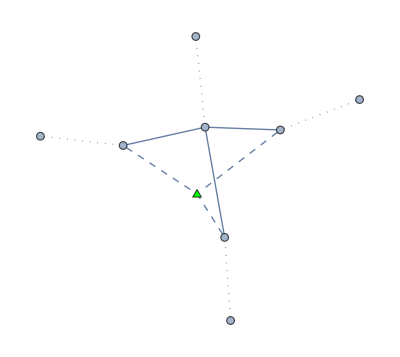

```mathematica
VisualizeDiagram[4,0,4,"Substitutions"-> "Analytics"]
```

## Integration

### Symbolic Integrand

The function IntegrandDiagram prints the integrands associated with these diagrams in terms of the internal momenta 𝓆[n] (the external momenta 𝓅[n] are by default put to zero). All the analytic functions appearing in the integrands correspond to propagators and other analytic functions corresponding to the subdiagrams that have been substituted.

We obtain the integrands for the simplified diagrams using the option "Substitutions"→ "Analytics" in IntegrandDiagram.

```mathematica
intgde4o4=IntegrandDiagram[4,0,4,"Substitutions"-> "Analytics"]
```

{ℬ[0]^3/8,1/2 ℬ[0] ℬ[𝓆[1]] 𝒢[𝓆[1]]^2,1/6 𝒢[𝓆[1]]^3 𝒮[𝓆[1]],2 ℬ[𝓆[1]] 𝒢[𝓆[1]] 𝒯[0,-𝓆[1],𝓆[1]],1/2 ℬ[𝓆[1]]^2 𝒢[𝓆[1]]^2,1/4 ℬ[𝓆[1]] 𝒬[0,-𝓆[1],0,𝓆[1]],1/2 ℬ[𝓆[1]]^2 𝒢[𝓆[1]]^2,1/3 𝒢[𝓆[1]] 𝒢[𝓆[2]] 𝒢[𝓆[1]+𝓆[2]] 𝒯[-𝓆[1]-𝓆[2],𝓆[1],𝓆[2]]}

### Explicit Integrand in Three Dimensions

The function WriteExplicit applied to the previous output prints the integrands in three dimensions in a form ready to be integrated. It does so by substituting each subdiagram block with its explicit analytic expression and by writing the internal moment in spherical components in 3D. With the option "Simplification"→"Simplify" also a Simplify is applied to them.

```mathematica
intgd3De4o4=WriteExplicit[intgde4o4,"Simplification"->"Simplify"]
```

{1/(4096 π^3),ArcTan[(𝓆[1]_ρ)/2]/(64 π^2 𝓆[1]_ρ (1+(𝓆[1]_ρ)^2)^2),-(-2+Log[1/9 (9+(𝓆[1]_ρ)^2)]+(6 ArcTan[(𝓆[1]_ρ)/3])/(𝓆[1]_ρ))/(192 π^2 (1+(𝓆[1]_ρ)^2)^3),ArcTan[(𝓆[1]_ρ)/2]/(16 π^2 𝓆[1]_ρ (1+(𝓆[1]_ρ)^2) (4+(𝓆[1]_ρ)^2)),ArcTan[(𝓆[1]_ρ)/2]^2/(32 π^2 (𝓆[1]_ρ)^2 (1+(𝓆[1]_ρ)^2)^2),ArcTan[(𝓆[1]_ρ)/2]/(64 π^2 𝓆[1]_ρ (4+(𝓆[1]_ρ)^2)^2),ArcTan[(𝓆[1]_ρ)/2]^2/(32 π^2 (𝓆[1]_ρ)^2 (1+(𝓆[1]_ρ)^2)^2),ArcTan[(𝓆[1]_ρ 𝓆[2]_ρ √((𝓆[1]_ρ)^2+2 Cos[𝓆[2]_θ] 𝓆[1]_ρ 𝓆[2]_ρ+(𝓆[2]_ρ)^2+4 Sin[𝓆[2]_θ]^2))/(2 (4+(𝓆[1]_ρ)^2+Cos[𝓆[2]_θ] 𝓆[1]_ρ 𝓆[2]_ρ+(𝓆[2]_ρ)^2))]/(12 π 𝓆[1]_ρ (1+(𝓆[1]_ρ)^2) 𝓆[2]_ρ (1+(𝓆[2]_ρ)^2) (1+(𝓆[1]_ρ)^2+2 Cos[𝓆[2]_θ] 𝓆[1]_ρ 𝓆[2]_ρ+(𝓆[2]_ρ)^2) √((𝓆[1]_ρ)^2+2 Cos[𝓆[2]_θ] 𝓆[1]_ρ 𝓆[2]_ρ+(𝓆[2]_ρ)^2+4 Sin[𝓆[2]_θ]^2))}

Notice that, due to the spherical symmetry, the angular components of 𝓆[1], together with 𝓆[2]_("ϕ") do not appear in the above expression.

### Residual Loops

Some of these integrands can be integrated analytically, while others not. So let's define a generic function to integrate them numerically. First of all, we have to understand in each case on how many variables we have to integrate. The function CountLoops gives the number of residual loops on which we have to integrate.

```mathematica
loope4o4=CountLoops/@intgd3De4o4
```

{0,1,1,1,1,1,1,2}

### Integration in Three Dimensions

Let us write a function for the numerical integration of diagrams with 0, 1, and 2 residual loops. Our integrals will be 0, 1, and 3 dimensional, respectively.

Particular care has to be taken for the integral's measure. We need to consider a factor 1/(2 π)^3 for every loop, and, since we are in spherical coordinates, a factor 1/2 (𝓆(n))_("ρ")^2 sin((𝓆(n))_("θ")) for every loop. Notice that we do not need to integrate over 𝓆[1]_("θ"),  𝓆[1]_("ϕ"), and 𝓆[2]_("ϕ") and the corresponding factor can be taken into account analytically. Thus we can write:

```mathematica
nintegratedim[l_,intgr_]:=Module[{intsimpl,out},
Which[
l==0,intgr,
l==1,intsimpl=Simplify[intgr Subscript[𝓆[1], "ρ"]^2/(2 π^2)];NIntegrate[intsimpl,{Momentum[1,"ρ"] ,0,∞}],
l==2,intsimpl=Simplify[intgr Subscript[𝓆[1], "ρ"]^2/(2 π^2)Subscript[𝓆[2], "ρ"]^2/(2 π^2)Sin[Subscript[𝓆[2], "θ"]]/2
];NIntegrate[intsimpl,{Momentum[1,"ρ"] ,0,∞},{Momentum[2,"ρ"] ,0,∞},{Momentum[2,"θ"] ,0,π}]
]]
```

Disclaimer: the integration variables in the Mathematica function NIntegrate must be written as above with the FullForm Momentum[i, "sub"], or, if using the short notation 𝓆 for the variables, one needs to use Evaluate as follows NIntegrate[intsimpl,Evaluate@{𝓆[1]_("ρ") ,0,∞}].

Now we can perform the integrations:

```mathematica
results3De4o4=Table[nintegratedim[loope4o4⟦i⟧,intgd3De4o4⟦i⟧],{i,Length@loope4o4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.65141×10^-6 and 5.33404×10^-12 for the integral and error estimates.

{1/(4096 π^3),0.0000209971,-3.95607×10^-7,0.0000483239,0.0000163598,7.87391×10^-6,0.0000163598,3.65141×10^-6}

Note that the numerical integration in three dimensions requires a bit more care if one wants to achieve a greater level of accuracy.
We can now compare these values with those that can be printed using the function ValueDiagram. There is a normalization factor of  (16 π)^(v4-1) to obtain the Nickel normalization.

```mathematica
ValueDiagram[4, 0, 4]
```

{1,8/3,1/3 (1-8 Log[2]+Log[81]),64/3 Log[4/3],2.077724965342882816003454391.×10^-25,1,2.077724965342882816003454391.×10^-25,0.46373496176534064731.×10^-18}

```mathematica
(16π)^3 results3De4o4
N@ValueDiagram[4,0,4]
```

{1,2.66667,-0.0502428,6.13722,2.07772,1.,2.07772,0.463735}

{1.,2.66667,-0.0502428,6.13722,2.077724965342881.×10^-25,1.,2.077724965342881.×10^-25,0.4637349617653411.×10^-18}

Related Guides

Phi4tools

Related Tech Notes

Perturbative Series Generation